```mathematica
phi[x_] := a (Exp[I k x]+  Exp[- I k x])
```

```mathematica
Solve[
{phi[L] == 0, phi[-L] == 0},
{a,k}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{k→π/(2 L)}}

```mathematica
phi[x_] := a (Exp[n I π/(2L) x]- (-1)^n Exp[-n I π/(2L) x])
```

```mathematica
pdist = Simplify[phi[x]Conjugate[phi[x]], {{x, a,L}∈Reals, n ∈ Integers}]
```

a^2 ((-1)^(1+n)+ⅇ^((ⅈ n π x)/L)) Conjugate[(-1)^(1+n)+ⅇ^((ⅈ n π x)/L)]

```mathematica
Integrate[pdist, {x, -L,L}]
```

∫_-L^L a^2 ((-1)^(1+n)+ⅇ^((ⅈ n π x)/L)) Conjugate[(-1)^(1+n)+ⅇ^((ⅈ n π x)/L)]ⅆx

```mathematica
k[n_] := (π n)/(2L)
```

```mathematica
Integrate[x Sin[k[i] x]Cos[k[j] x], {x, -L, L}] /. Cos[(i π)/2] -> 0 /. Sin[(i π)/2] -> (-1)^((i-1)/2) /.Cos[(j π)/2] -> (-1)^(j/2) /. Sin[(j π)/2] -> 0
```

(8 ⅈ^(-1+i+j) (i^2+j^2) L^2)/((i-j)^2 (i+j)^2 π^2)

```mathematica
%//FullSimplify
```

-(8 ⅈ ⅈ^(i+j) (i^2+j^2) L^2)/((i^2-j^2)^2 π^2)

```mathematica
Integrate[x Sin[k[i] x]Cos[k[j] x], {x, -L, L}]
```

-(4 L^2 (i Cos[(i π)/2] ((i^2-j^2) π Cos[(j π)/2]+4 j Sin[(j π)/2])+Sin[(i π)/2] (-2 (i^2+j^2) Cos[(j π)/2]+j (i^2-j^2) π Sin[(j π)/2])))/((i-j)^2 (i+j)^2 π^2)

```mathematica
% /. i -> 11 /. j -> 20
```

-4168/(77841 π^2)

```mathematica
N[-4168/(77841 π^2)]
```

-0.00542525

```mathematica
2+x == x+1+1
```

True

```mathematica
const := (h^2 π^2)/(8 m L^2)
```

```mathematica
bigk = 10
```

10

```mathematica
(( 4 I^(i+j+1) h)/(m  π^2)) Sum[ (Exp[I const(i^2 - (2k)^2)t] ((2k)^2 - j^2) - Exp[I const ((2k)^2 - j^2) t] (i^2 - (2k)^2))(((i^2 + (2k)^2)((2k)^2 + j^2))/((i^2 - (2k)^2)^2 ((2k)^2 - j^2)^2)),{k, 1, 5}]/. i-> 3 /. j ->3 /. t-> 0 //N
```

0.-1.00646 ⅈ

```mathematica
b[i_/;EvenQ[i], j_/;EvenQ[j]]:= 
(- 4 I^(i+j+1) h)/(m  π^2) Sum[ (Exp[I const(i^2 - (2k+1)^2)t] ((2k+1)^2 - j^2) - Exp[I const ((2k+1)^2 - j^2) t] (i^2 - (2k+1)^2))((i^2 + (2k+1)^2)((2k+1)^2 + j^2))/((i^2 - (2k+1)^2)^2 ((2k+1)^2 - j^2)^2),{k, 0, bigk}]
```

```mathematica
b[i_/;OddQ[i], j_/;OddQ[j]]:= 
(4 I^(i+j+1) h)/(m  π^2) Sum[ (Exp[I const(i^2 - (2k)^2)t] ((2k)^2 - j^2) - Exp[I const ((2k)^2 - j^2) t] (i^2 - (2k)^2))((i^2 + (2k)^2)((2k)^2 + j^2))/((i^2 - (2k)^2)^2 ((2k)^2 - j^2)^2),{k, 1, bigk}]
```

```mathematica
b[_,_] := 0
```

```mathematica
bigkimp[i_,j_] := i+j;
bimp[i_/;EvenQ[i], j_/;EvenQ[j]]:= 
(4 I^(i+j+1) h)/(m  π^2) Sum[ (Exp[I const(i^2 - (2k+1)^2)t] ((2k+1)^2 - j^2) - Exp[I const ((2k+1)^2 - j^2) t] (i^2 - (2k+1)^2))((i^2 + (2k+1)^2)((2k+1)^2 + j^2))/((i^2 - (2k+1)^2)^2 ((2k+1)^2 - j^2)^2),{k, 0, bigkimp[i,j]}]
bimp[i_/;OddQ[i], j_/;OddQ[j]]:= 
-(4 I^(i+j+1) h)/(m  π^2) Sum[ (Exp[I const(i^2 - (2k)^2)t] ((2k)^2 - j^2) - Exp[I const ((2k)^2 - j^2) t] (i^2 - (2k)^2))((i^2 + (2k)^2)((2k)^2 + j^2))/((i^2 - (2k)^2)^2 ((2k)^2 - j^2)^2),{k, 1, bigkimp[i,j]}]
bimp[_,_] := 0
```

```mathematica
h = 1; m = 1/2; L = 1/2;
```

```mathematica
bigk=50
```

50

```mathematica
Evaluate[bimp[0,2]]
```

(4 ⅈ (5/9 (-3 ⅇ^(-1/8 ⅈ π^2 t)+ⅇ^(-3/8 ⅈ π^2 t))+13/225 (9 ⅇ^(5/8 ⅈ π^2 t)+5 ⅇ^(-9/8 ⅈ π^2 t))+(29 (25 ⅇ^(21/8 ⅈ π^2 t)+21 ⅇ^(-25/8 ⅈ π^2 t)))/11025))/π^2

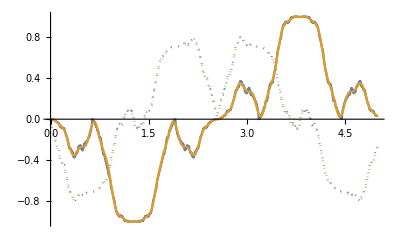

```mathematica
Module[{compiled = Compile[{{t,_Real}}, Evaluate[b[0,2]]],
compiledapprox = Compile[{{t,_Real}},Evaluate[bimp[0,2]]]},
ReImPlot[{compiled[t],compiledapprox[t]}, {t, 0, 5}]]
```

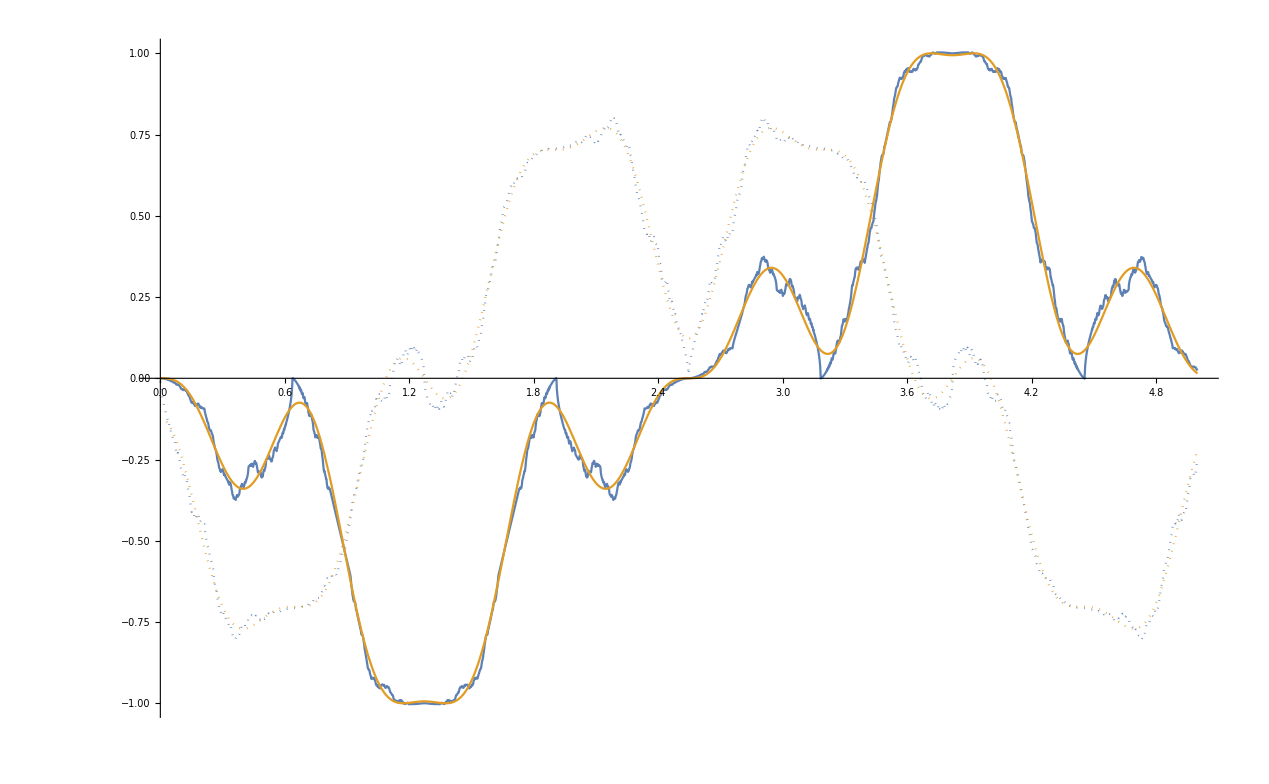

```mathematica
Module[{compiled = Compile[{{t,_Real}}, Evaluate[b[0,2]]],
compiledapprox = Compile[{{t,_Real}}, Evaluate[Block[{bigk = 1}, b[0,2]]]]},
ReImPlot[{compiled[t],compiledapprox[t]}, {t, 0, 5}]]
```

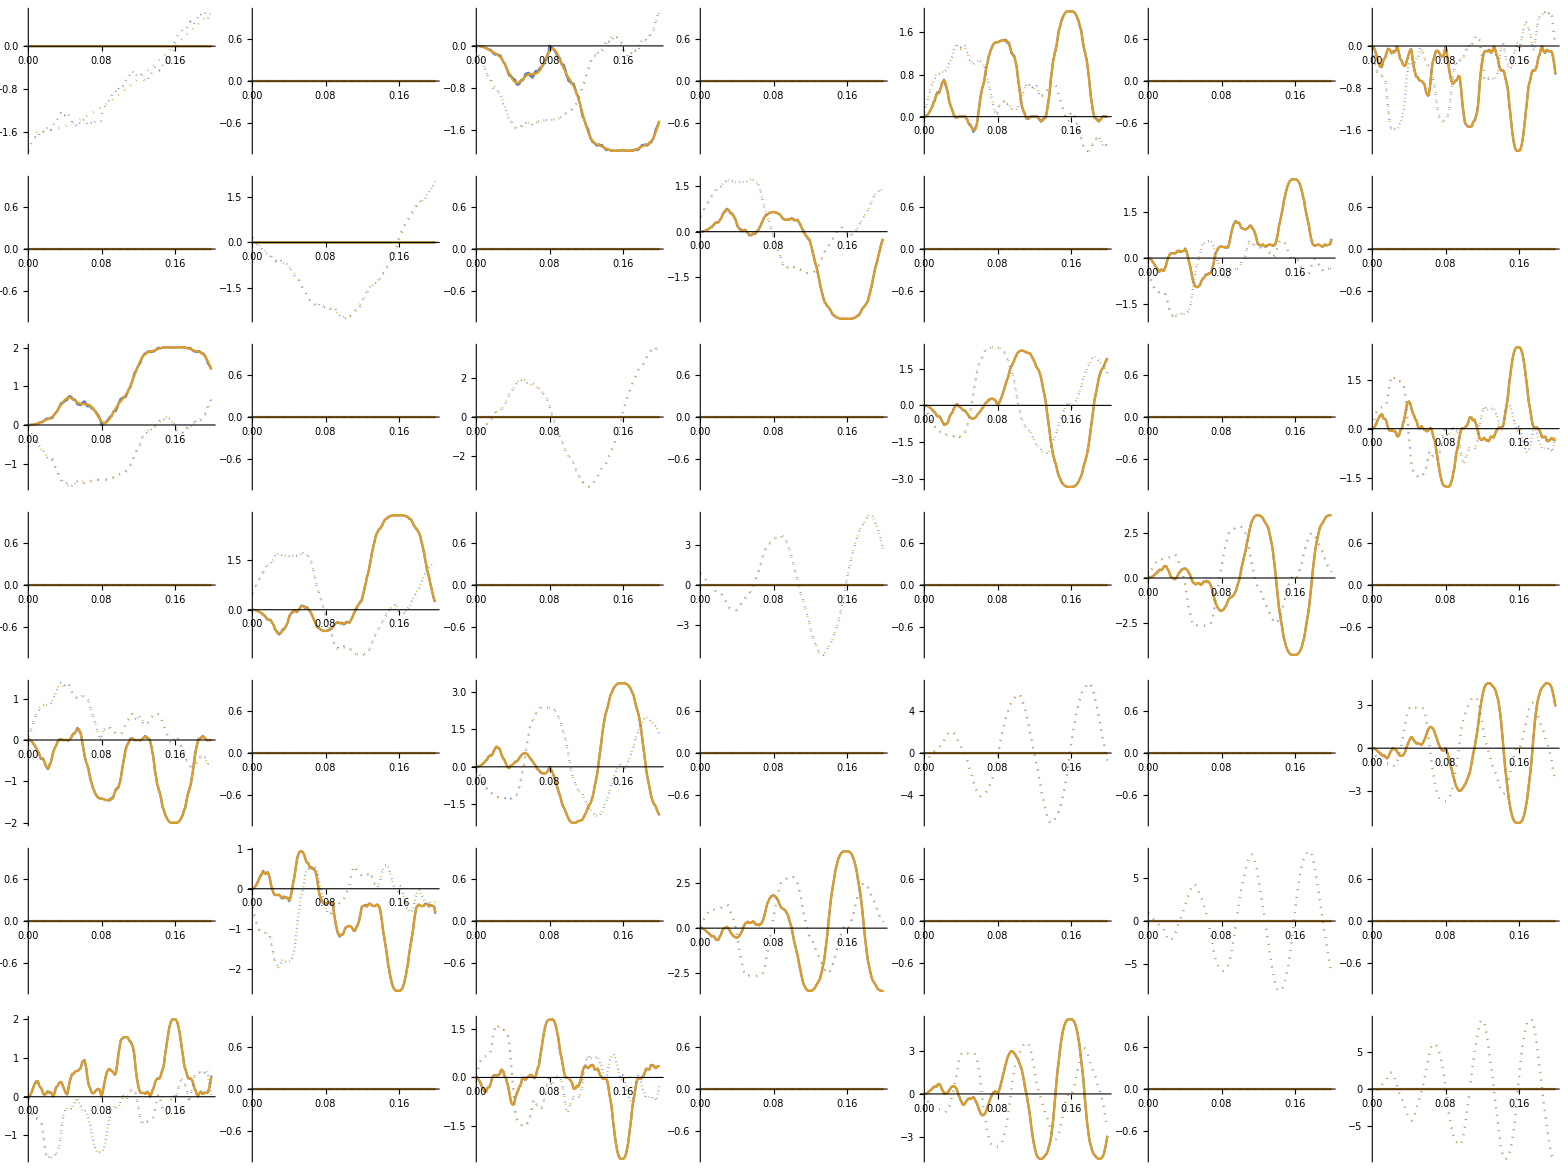

```mathematica
Table[
Module[{compiled = Compile[{{t,_Real}}, Evaluate[b[i,j]]],
compiledapprox = Compile[{{t,_Real}}, Evaluate[bimp[i,j]]]},
ReImPlot[{compiled[t],compiledapprox[t]}, {t, 0, .2}]], {i,0, 6},{j,0,6}] // TableForm
```

```mathematica
Table[
Module[{compiled = Compile[{{t,_Real}}, Evaluate[b[i,j]]],
compiledapprox = Compile[{{t,_Real}}, Evaluate[Block[{bigk = 2}, b[i,j]]]]},
ReImPlot[{compiled[t],compiledapprox[t]}, {t, 0, 5}]], {i, 0, 8},{j,0,8}] // TableForm
```

```mathematica
bigk = 1
```

1

```mathematica
Table[
Module[{compiled = Compile[{{t,_Real}}, Evaluate[b[i,j]]]},
ReImPlot[compiled[t], {t, 0, 5}]], {i, 0, 8},{j,0,8}] // TableForm
```

```mathematica
comp[0.2]
```

0.-0.779388 ⅈ

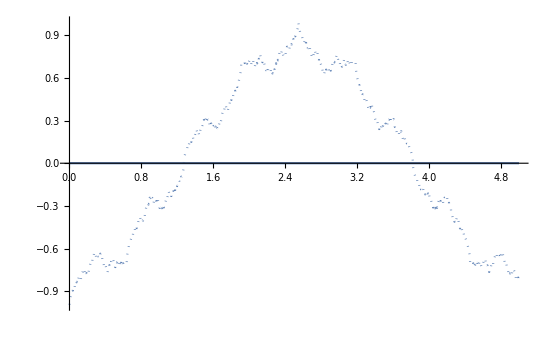

```mathematica
ReImPlot[comp[t], {t, 0, 5}]
```

```mathematica
bigk = 10
```

10

CompiledFunction[…]

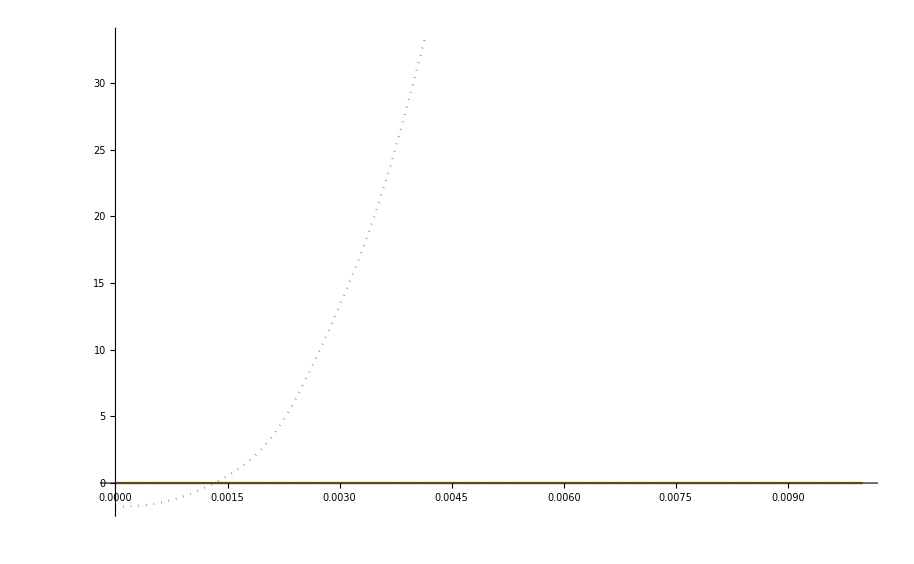

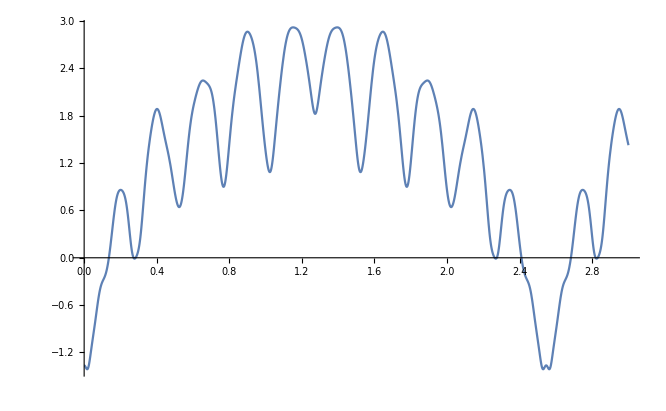

```mathematica
c2[n_]:= Sum[-b[n,k1]b[k1,k2]b[k2,k3]b[k3,k4]b[k4,n], {k1, 0, bigk}, {k2, 0, bigk}, {k3,0,bigk}, {k4,0,bigk}];
expr = Compile[{t}, Evaluate[c2[1]]]
ReImPlot[{expr[t], -b[1,1]^5}, {t, 0, 0.01}]
```

```mathematica
bigk
```

30

```mathematica
k
```

k

```mathematica
L=.; h=.; m=.;
```

```mathematica
Integrate[Cos[k[n]x]^2, {x, -L,L}]
```

L+(L Sin[n π])/(n π)